```mathematica
ClearAll["`*"]
Clear[Derivative]
δ = 0.7;
ω = √(34.5/67);
 r1 = NDSolve[{x'[t] == v[t], v'[t] == -2δ*v[t] - ω^2*x[t], x[0] == 10, x'[0] == 0}, {x, v}, {t, 0, 20}];
```

NDSolve::icordinit: The initial values for all the dependent variables are not explicitly specified. NDSolve will attempt to find consistent initial conditions for all the variables.

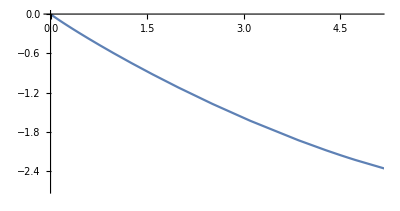

```mathematica
ParametricPlot[Evaluate[{x[t], x'[t]} /. r1], {t,0,20}]
```